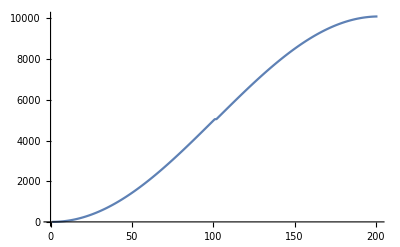

```mathematica
pathToSolutions=FileNameJoin[{NotebookDirectory[],"dataOut/solutionMatrix.csv"}];
solutions=Import[pathToSolutions,"Table"];
pathToEigenvalues=FileNameJoin[{NotebookDirectory[],"dataOut/eigenvalueArray.csv"}];
eigenvalues=Import[pathToEigenvalues,"Table"];
ListLinePlot[eigenvalues]
```

```mathematica
HarmonicOscillatorψ[n_,x_,m_,ω_,ℏ_]:=((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))HermiteH[n,√((m ω)/ℏ)x] ⅇ^(-(m ω)/(2 ℏ)x^2);
```

```mathematica
Manipulate[
ListLinePlot[solutions[[i]],DataRange->{0,4},PlotRange->All],
{{i,71},1,100,1}
]
```

```mathematica
ListPlot3D[solutions,AxesLabel->{"x","n"}, DataRange->{{0,4},{0,200}}, PlotRange->{{0,4},{0,100},All}]
```

-Graphics3D-

## Time dependence of the Jacobi Method

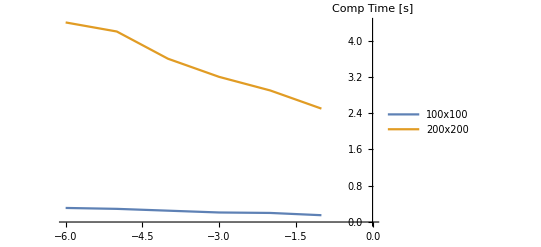
-Graphics-Log of Tolerence for Off-Diagonals

```mathematica
Labeled[
ListLinePlot[{
{{-6,0.31},
{-5,0.29},
{-4,0.25},
{-3,0.21},
{-2,0.20},
{-1,0.15}},
{{-6,4.4},
{-5,4.2},
{-4,3.6},
{-3,3.2},
{-2,2.9},
{-1,2.5}}
},AxesLabel->{"","Comp Time [s]"},PlotLegends->{"100x100","200x200"}],
"Log of Tolerence for Off-Diagonals"]
```

FittedModel[1.00434^(2.18273 x)]

FittedModel[8.89186×10^-7 x^3]

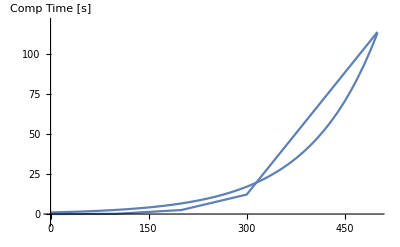
-Graphics-Matrix Size

```mathematica
data={
{0,0},
{100,0.15},
{200,2.5},
{300,12.2},
{500,114}
};
fit=NonlinearModelFit[data,b^(c*x),{a,b,c},x]
fit2=NonlinearModelFit[data,a x^3,{a,b},x]
Labeled[
Show[
Plot[fit[x],{x,0,500},PlotRange->{All,{-5,120}},AxesLabel->{"","Comp Time [s]"}],
ListLinePlot[data]
],
"Matrix Size"]
```